```mathematica
folder = "/Users/AaronLopes/Desktop/newsela_article_corpus/articles/";
```

```mathematica
filesPath=FileNames["*.en.*.txt",folder];
```

```mathematica
path=RandomChoice[filesPath]
```

/Users/AaronLopes/Desktop/newsela_article_corpus/articles/dye-library.en.0.txt

```mathematica
0.009*Length@filesPath
```

86.085

```mathematica
(*Classify en text as 2-5 simple, 6-12 complex*)
```

```mathematica
Normal@metadata[[1]]
```

<|slug→10dollarbill-woman,language→en,title→Tubman, Perkins or Roosevelt? Woman on $10 bill campaign begins,gradelevel→12.,version→0,filename→10dollarbill-woman.en.0.txt|>

```mathematica
Normal@GroupBy[metadata, #gradelevel≤6.0&]
```

GroupBy::list1: The argument metadata is not a valid list of Associations or rules or lists of rules.

GroupBy[metadata,#gradelevel≤6.&]

```mathematica
lowLevelFileNames=Lookup[Lookup[Normal@GroupBy[metadata, #gradelevel≤6.0&],False], "filename"];
highLevelFileNames=Lookup[Lookup[Normal@GroupBy[metadata, #gradelevel≤6.0&],True], "filename"];
```

```mathematica
(*Search for filename in low level category*)
```

```mathematica
lowtext = Select[lowLevelFileNames,StringMatchQ["10dollarbill-woman.en."~~DigitCharacter~~".txt"]];
```

```mathematica
(*Construct filepath*)
```

```mathematica
text = StringJoin[folder,#]&/@lowtext;
```

```mathematica
(*Import text from filepath, obtain list of filenames*)
```

```mathematica
randCorpusLow = Import[#]&/@text;
```

```mathematica
hightext = Select[highLevelFileNames,StringMatchQ["10dollarbill-woman.en."~~DigitCharacter~~".txt"]];
```

```mathematica
text = StringJoin[folder,#]&/@hightext;
```

```mathematica
randCorpusHigh = Import[#]&/@text;
```

```mathematica
TextSentences[randCorpusHigh, 5]
```

{{WASHINGTON — It's time for a woman to be honored on American money, U.S. Treasury Secretary Jacob J. Lew said.,The all-male lineup has gone on long enough.,"We will right that wrong," Lew said.,"And when the new, redesigned $10 note is released, it will bear the portrait of a woman.",Who are some of the candidates to be  the first woman on U.S. currency notes in more than a century?},{WASHINGTON — It is time that a woman be on American money, the head of the U.S. Treasury Department said.,"We will right that wrong," Treasury Secretary Jacob J. Lew promised.,The new $10 bill will include the picture of a woman.,Who are some of the candidates to be  the first woman on American paper money in more than a century?,A former slave who helped to end slavery.},{WASHINGTON — Pictures of men are on all American paper money.,It is time for a woman's face, a top government worker said.,"We will right that wrong," Jacob J. Lew said.,He is the head of Treasury Department.,It prints money for the American government.}}

```mathematica
TextSentences[randCorpusLow,5]
```

{{WASHINGTON — An abolitionist.,The longest-serving first lady.,The Labor secretary through the Great Depression.,The founder of the Girl Scouts.,These are some of the candidates to be the first woman on U.S. currency notes in more than a century.},{WASHINGTON — The all-male lineup on American money has gone on long enough, Treasury Secretary Jacob J. Lew said.,"We will right that wrong, and when the new, redesigned $10 note is released, it will bear the portrait of a woman," he said in Washington, D.C., recently.,Who are some of the candidates to be the first woman on U.S. currency notes in more than a century?,A former slave who worked to abolish slavery.,The longest-serving first lady.}}

```mathematica
avglowt= WordCount[randCorpusLow]/Length[randCorpusLow]
```

{925/2,925/2}

```mathematica
metadata = Import["/Users/AaronLopes/Desktop/newsela_article_corpus/articles_metadata.csv","Dataset","HeaderLines"->1];
outcomplex = metadata[[All,{"gradelevel","filename"}]][Select[#gradelevel==12.0||#gradelevel==11.0||#gradelevel==10.0||#gradelevel==9.0||#gradelevel==8.0||#gradelevel==7.0||#gradelevel==6.0&]];
outsimple = metadata[[All,{"gradelevel","filename"}]][Select[#gradelevel==5.0||#gradelevel==4.0||#gradelevel==3.0||#gradelevel==2.0&]];
```

```mathematica
filescomplex= "/Users/AaronLopes/Desktop/newsela_article_corpus/articles/"<>outcomplex[[#]][[2]]&/@Range[Length[outcomplex]];
filessimple = "/Users/AaronLopes/Desktop/newsela_article_corpus/articles/"<>outsimple[[#]][[2]]&/@Range[Length[outsimple]];
complexcorpus= Import[#]&/@(filescomplex[[1;;30]]);
simplecorpus = Import[#]&/@(filessimple[[1;;30]]);
```

```mathematica
(*data analysis/preprocessing*)
```

```mathematica
avgcomplexwrds=  WordCount[complexcorpus]/Length[complexcorpus];
```

```mathematica
N[Total[avgcomplex]]
```

800.4

```mathematica
avgsimplewrds = WordCount[simplecorpus]/Length[simplecorpus];
```

```mathematica
N[Total[avgsimple]]
```

530.3

```mathematica
(*word frequency in complex/simple files*)
```

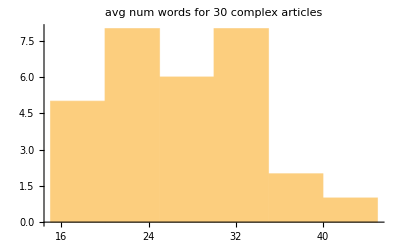

```mathematica
Histogram[avgcomplexwrds,PlotLabel->"avg num words for 30 complex articles"]
```

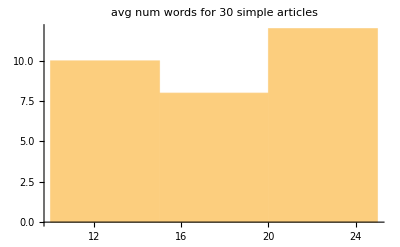

```mathematica
Histogram[avgsimplewrds,PlotLabel->"avg num words for 30 simple articles"]
```

```mathematica
(*Random Sampling*)
```

```mathematica
outcomplex//List
```

{Dataset[<>]}

```mathematica
(*random sentence sample 1 file*)
```

```mathematica
outcomplex = metadata[[All,{"gradelevel","filename"}]][Select[#gradelevel==12.0||#gradelevel==11.0||#gradelevel==10.0||#gradelevel==9.0||#gradelevel==8.0||#gradelevel==7.0||#gradelevel==6.0&]];
```